```mathematica
Solution @ 4  levels, excitation from 5s to nd,  Bloch equations in steady state
```

WorkingPrecision→2 MachinePrecision

(0 | -Im[Ωp]/2+Re[Ωp]/2 | 0 | -Im[ΩL]/2+Re[ΩL]/2
Im[Ωp]/2+Re[Ωp]/2 | -δp | -Im[Ωmw]/2+Re[Ωmw]/2 | 0
0 | Im[Ωmw]/2+Re[Ωmw]/2 | -δmw-δp | -Im[Ωc]/2+Re[Ωc]/2
Im[ΩL]/2+Re[ΩL]/2 | 0 | Im[Ωc]/2+Re[Ωc]/2 | δc-δmw-δp)

(γ2 Reρ[2,2][t]+γ4 Reρ[4,4][t] | -1/2 γ2 Reρ[1,2][t]-γ2d Reρ[1,2][t] | -1/2 γ3 Reρ[1,3][t]-γ3d Reρ[1,3][t] | -1/2 γ4 Reρ[1,4][t]
-1/2 γ2 Reρ[1,2][t]-γ2d Reρ[1,2][t] | -γ2 Reρ[2,2][t]+γ3 Reρ[3,3][t] | -γ2d Reρ[2,3][t]-γ3d Reρ[2,3][t]+1/2 (-γ2 Reρ[2,3][t]-γ3 Reρ[2,3][t]) | -γ2d Reρ[2,4][t]+1/2 (-γ2 Reρ[2,4][t]-γ4 Reρ[2,4][t])
-1/2 γ3 Reρ[1,3][t]-γ3d Reρ[1,3][t] | -γ2d Reρ[2,3][t]-γ3d Reρ[2,3][t]+1/2 (-γ2 Reρ[2,3][t]-γ3 Reρ[2,3][t]) | -γ3 Reρ[3,3][t] | -γ3d Reρ[3,4][t]+1/2 (-γ3 Reρ[3,4][t]-γ4 Reρ[3,4][t])
-1/2 γ4 Reρ[1,4][t] | -γ2d Reρ[2,4][t]+1/2 (-γ2 Reρ[2,4][t]-γ4 Reρ[2,4][t]) | -γ3d Reρ[3,4][t]+1/2 (-γ3 Reρ[3,4][t]-γ4 Reρ[3,4][t]) | -γ4 Reρ[4,4][t])

1 | Reρ[1,1][t]
2 | Reρ[2,2][t]
3 | Reρ[3,3][t]
4 | Reρ[4,4][t]
5 | Reρ[1,2][t]
6 | Reρ[1,3][t]
7 | Reρ[1,4][t]
8 | Reρ[2,3][t]
9 | Reρ[2,4][t]
10 | Reρ[3,4][t]
11 | Imρ[1,2][t]
12 | Imρ[1,3][t]
13 | Imρ[1,4][t]
14 | Imρ[2,3][t]
15 | Imρ[2,4][t]
16 | Imρ[3,4][t]

1

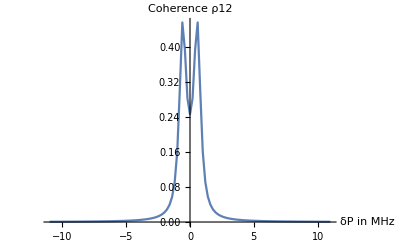

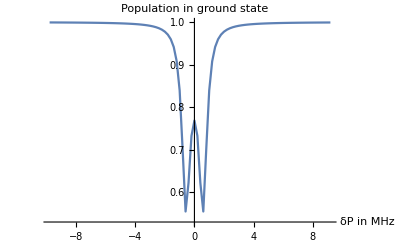

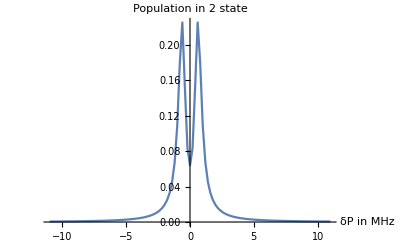

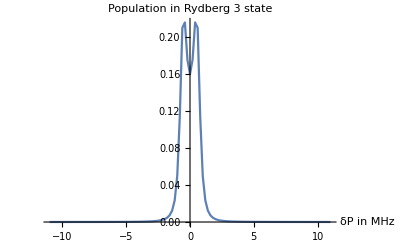

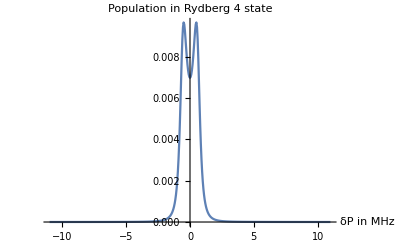

{1,1}

{2,2}

{3,3}

{4,4}

{5,5}

{6,6}

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[Null, 1].

{1,2}

{1,3}

{1,4}

{1,5}

{1,6}

{2,3}

{2,4}

{2,5}

{2,6}

{3,4}

{3,5}

{3,6}

{4,5}

{4,6}

{5,6}

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[Null, 1].

{1,2}

{1,3}

{1,4}

{1,5}

{1,6}

{2,3}

{2,4}

{2,5}

{2,6}

{3,4}

{3,5}

{3,6}

{4,5}

{4,6}

{5,6}

Join::heads: Heads Flatten and List at positions 1 and 3 are expected to be the same.

Join[Flatten[Null,1],Flatten[Null,1],{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}]

```mathematica
WorkingPrecision->(2 MachinePrecision)
ϵ0=8.85*10^(-12);
c=2.9979*10^8;
h=6.626*10^(-34);
q=1.602*10^(-19);
a0=0.5292*10^(-10);
Eua=4.36*10^(-18); (*Hartree Energy*)
hbar=ℏ=h/(2π);
μm=10^(-6);
λp=0.319 10^-6;
σ0=3 λp^2/(2 π);
tau=200;(*ns*)


ClearAll[Nblevels,σ0,Delta, GammaSpont,δc,δP,δmw,Reρ,Imρ,Y2,MM2,γ2,γ3,ρ1S,ρ2S,ρ3S,ρ4S,Imρ12S,Imρ14S,γ4,Reρ23S,Reρ34S,ReH,ImH, γ2d,γ3d,Tab1,elcharge]

Nblevels=4;
ReH={{0,Re[Ωp]/2,0,Re[ΩL]/2},{Re[Ωp]/2,0,Re[Ωmw]/2,0},{0,Re[Ωmw]/2,0,Re[Ωc]/2},{Re[ΩL]/2,0,Re[Ωc]/2,0}};
ImH={{0,(-Im[Ωp])/2,0,(-Im[ΩL])/2},{Im[Ωp]/2,0,(-Im[Ωmw])/2,0},{0,Im[Ωmw]/2,0,-Im[Ωc]/2},{Im[ΩL]/2,0,Im[Ωc]/2,0}};

Reρρ[t_]=Table[Reρ[i,j][t],{i,Nblevels},{j,1,Nblevels}];
Do[
Reρ[i,j][t]=Reρ[j,i][t],
{i,Nblevels},{j,1,i-1}
];

Imρρ[t_]=Table[Imρ[i,j][t],{i,Nblevels},{j,1,Nblevels}];
Do[
Imρ[i,j][t]=-Imρ[j,i][t],
{i,Nblevels},{j,1,i-1}
];

Do[Imρ[i,i][t]=0,{i,1,Nblevels}];
Delta =- DiagonalMatrix[{0,δp,(δp+δmw),(δp+δmw-δc)}];
ReH=ReH+Delta;
Delta//MatrixForm;
ReH//MatrixForm;
ImH//MatrixForm;
(*Total Hamiltonian*)
TotalH=ReH+ImH//MatrixForm
(Reρρ[0] + Imρρ[0])//MatrixForm;
ReB=(ReH.Imρρ[t]-Imρρ[t].ReH)+(ImH.Reρρ[t]-Reρρ[t].ImH);
ImB=-(ReH.Reρρ[t]-Reρρ[t].ReH)+(ImH.Imρρ[t]-Imρρ[t].ImH);

GammaSpont=IdentityMatrix[Nblevels];
GammaSpont[[1,1]]=0;
GammaSpont[[2,2]]=γ2;
GammaSpont[[3,3]]=γ3;
GammaSpont[[4,4]]=γ4;


ReLoss=-1/2(GammaSpont.Reρρ[t]+Reρρ[t].GammaSpont);
ReLoss//MatrixForm;
ImLoss=-1/2(GammaSpont.Imρρ[t]+Imρρ[t].GammaSpont);
ImLoss//MatrixForm;

ReLoss[[2,2]]=(ReLoss[[2,2]]+γ3 Reρ[3,3][t]);
ReLoss[[1,1]]=ReLoss[[1,1]]+γ2 Reρ[2,2][t]+γ4 Reρ[4,4][t];


For[ii=1, ii≤ 4, ii++,
If[ii≠ 2,
ReLoss[[2,ii]]-= γ2d Reρ[2,ii][t];
ReLoss[[ii,2]]-= γ2d Reρ[2,ii][t];
ImLoss[[ii,2]]-=γ2d Imρ[ii,2][t];
ImLoss[[2,ii]]+=γ2d Imρ[ii,2][t];
]
]

For[ii=1, ii≤ 4, ii++,
If[ii≠ 3,
ReLoss[[3,ii]]-= γ3d Reρ[3,ii][t];
ReLoss[[ii,3]]-= γ3d Reρ[3,ii][t];
ImLoss[[ii,3]]-=γ3d Imρ[ii,3][t];
ImLoss[[3,ii]]+=γ3d Imρ[ii,3][t];
]
]
(*退相干项和自发辐射*)
ReLoss//MatrixForm
ReA=FullSimplify[ReB+ReLoss];
ImA=FullSimplify[ImB+ImLoss];
ReA//MatrixForm;
(ReB+ReLoss)//MatrixForm;
eqnsDifRe2=Flatten[
Table [
Simplify[ReA[[i,j]]==0,(Reρ[i,j][t])∈Reals&&(Imρ[i,j][t])∈Reals&&(Reρ[j,i][t])∈Reals&&(Imρ[j,i][t])∈Reals],
{i,1,Nblevels},{j,i,Nblevels}
]
];
eqnsDifIm1=Flatten[Table [Simplify[ImA[[i,j]]==0,(Reρ[i,j][t])∈Reals&&(Imρ[i,j][t])∈Reals&&(Reρ[j,i][t])∈Reals&&(Imρ[j,i][t])∈Reals],{i,1,Nblevels},{j,i+1,Nblevels}]];
eqnstime=Join[eqnsDifRe2,eqnsDifIm1];
eqnstime[[1]];
VariablesSolve2=Join[
Flatten[Table[(Reρ[i,i][t]),{i,1,Nblevels}]],
Flatten[Table[(Reρ[i,j][t]),{i,1,Nblevels},{j,i+1,Nblevels}]],
Flatten[Table[(Imρ[i,j][t]),{i,1,Nblevels},{j,i+1,Nblevels}]]
];

variablesList=Table[
{ii,VariablesSolve2[[ii]]},
{ii,1,Length[VariablesSolve2]}
];
variablesList//TableForm
MatrixCoef2=CoefficientArrays[eqnstime,VariablesSolve2];
MM2=Normal[MatrixCoef2][[2]];
Y2=-Normal[MatrixCoef2][[1]];
eqnsDifRe2check=MM2.VariablesSolve2;
Coef2=-Simplify[ReA[[1,1]]/eqnsDifRe2check[[1]]](*get rid off the scaling coefficient due to CoefficientArrays*)
MM2=MM2*Coef2;
Y2=-Y2*Coef2;
Y2[[1]]=1;
MM2[[1]]=Table[0,{i,1,Length[VariablesSolve2]}];
MM2[[1]][[1;;Nblevels]]=Table[1,{i,1,Nblevels}];
MM2//MatrixForm;
Y2//MatrixForm;
Length[VariablesSolve2];
solution:=LinearSolve[MM2,Y2];
ρ1S:=solution[[1]];
ρ2S:=solution[[2]];
ρ3S:=solution[[3]];
ρ4S:=solution[[4]];
Imρ12S:=solution[[11]]
Imρ14S:=solution[[13]];
Imρ23S:=solution[[14]];
Imρ34S:=solution[[16]];
Reρ12S:=solution[[5]];
Reρ14S:=solution[[7]];
Reρ23S:=solution[[8]];
Reρ34S:=solution[[10]];

γ4=2π 5.22*10^-3; γ3= 2π 0.1 10^-3; γ2=2π 0.2 10^-3; γ2d=2π 0.01 10^-3;
γ3d=0.01 2π 10^-3;
Ωc=2π 1.1 10^-3;Ωmw=2π 1.2 10^-3;
δc=0.0000*2π*10^-3;
δmw=00.0000*2π*10^-3;δp=0.00*2π*10^-3;
Ωp=2π 0.5 10^-3;ΩL=0;

Tab7=Table[{δp/(2π)10^3,Imρ12S*(γ2/Ωp)^-1},{δp,-11*2π*10^-3,11*2π*10^-3,0.2*2π*10^-3}];
ListLinePlot[Tab7,PlotRange->All,AxesLabel->{"δP in MHz","Coherence ρ12"}]
Tab6=Table[{δp/(2π)10^3,ρ1S},{δp,-9.8*2π*10^-3,9.2*2π*10^-3,0.2*2π*10^-3}];
ListLinePlot[Tab6,PlotRange->All,AxesLabel->{"δP in MHz","Population in ground state"}]
Tab1=Table[{δp/(2π)10^3,ρ2S},{δp,-11*2π*10^-3,11*2π*10^-3,0.2*2π*10^-3}];
ListLinePlot[Tab1,PlotRange->All,AxesLabel->{"δP in MHz","Population in 2 state"}]

Tab2=Table[{δp/(2π)10^3,ρ3S},{δp,-11*2π*10^-3,11*2π*10^-3,0.2*2π*10^-3}];
ListLinePlot[Tab2,PlotRange->All,AxesLabel->{"δP in MHz","Population in Rydberg 3 state"}]

Tab3=Table[{δp/(2π)10^3,ρ4S},{δp,-11*2π*10^-3,11*2π*10^-3,0.05*2π*10^-3}];
ListLinePlot[Tab3,PlotRange->All,AxesLabel->{"δP in MHz","Population in Rydberg 4 state"}]
```

```mathematica
Propagation with  wave mixing
```

```mathematica
ClearAll[Ip,nat,wz,sxp,sxp2,sxp3,sxp4,sxp6,sxp7,sxp7b,sxp7c,Ipout,ReΩpout,Is,wp,Δp,Ωm10,Grr,Om,Ωpout,Ωsignal,Ωm,sxp6b,Ωm20,Ωmw1,Ωs]

sxp[Ip_,nat_,wz_]:=Module[{Ipout=Ip,zz=-1.5wz,Deltazz=wz/20},While[(zz<(1.5wz)),Ipout=Ipout-Deltazz*ⅇ^(-2 zz^2/wz^2)*nat*γ2*10^9*h*c/(λp)*Re[ρ2S];Ωp=γ2 √(Ipout/(2 Is));zz=zz+Deltazz];Ipout]
sxp3[Ip_,nat_,wz_]:=Module[{Ipout=Ip,zz=-1.5wz,Deltazz=wz/40,Ωpout=γ2*10^9 √(Ip/(2 Is))},While[(zz<(1.5wz)),Ωp=Ωpout/10^9;Ωpout=Ωpout-Deltazz*ⅇ^(-2 zz^2/wz^2)*nat*((γ2*10^9)^2)/(4 Is)*(h*c)/λp*Imρ12S;zz=zz+Deltazz];Ipout=2 Is((Abs[Ωpout]/10^9)^2)/γ2^2]

sxp4[Ip_,nat_,wz_]:=Module[{Ipout=Ip,zz=-1.5wz,Deltazz=wz/40,Ωpout=γ2*10^9 √(Ip/(2 Is))},While[(zz<(1.5wz)),Ωp=Ωpout/10^9;ΩL=0;Ωpout=Ωpout-Deltazz*ⅇ^(-2 zz^2/wz^2)*nat*(γ2*10^9)*(6π)/2*(λp/(2π))^2*(Imρ12S +ⅈ Reρ12S);zz=zz+Deltazz];Ipout=2 Is((Abs[Ωpout]/10^9)^2)/γ2^2]
sxp6[Ip_,nat_,wz_]:=Module[{Iout,zz=-1.5wz,Deltazz=wz/30,Ωpout=γ2*10^9 √(Ip/(2 Is)),ΩLSignal=0,IpSignal},While[(zz<(1.5wz)),Ωp=Ωpout/10^9;
ΩL=ΩLSignal/10^9;Ωpout=Ωpout-Deltazz*ⅇ^(-2 zz^2/wz^2)*nat*(γ2*10^9)*(6π)/2*(λp/(2π))^2*(Imρ12S +ⅈ Reρ12S);
ΩLSignal=ΩLSignal-Deltazz*ⅇ^(-2 zz^2/wz^2)*nat*(γ4*10^9)*(6π)/2*(λL/(2π))^2*(Imρ14S +ⅈ Reρ14S)/6;

zz=zz+Deltazz];Iout={6*2 Is((Abs[ΩLSignal]/10^9)^2)/γ4^2,2 Is((Abs[Ωpout]/10^9)^2)/γ2^2}]

sxp6b[Ip_,nat_,wz_,Ωmw0_]:=Module[{Iout,zz=-1.5wz,Deltazz=wz/100,Ωpout=γ2*10^9 √(Ip/(2 Is)),ΩLSignal=0*10^-3*2π*10^9,Ωmw2=Ωmw0,IpSignal},While[(zz<(1.5wz)),Ωp=Ωpout/10^9;
(*Print[Ωc1 10^3/(2π)];
Print[Ωc2 10^3/(2π)];
Print[Ωmw2 10^3/(2π)];
Print[Ωmw1 10^3/(2π)];
Print[Ωs 10^3/(2π)];
Print[Imρ16S ];
Print[Abs[Ωmw2] 10^3/(2π)];*)
(*d12=2.99*q*a0;
ωp=2π c/λp;
ηp= (d12^2*ωp)/(2 ϵ0 ℏ c);
Print[(γ5p32*10^9)*(6π)/2*(λp/(2π))^2," ",2ηp];*)
ΩL=ΩLSignal/10^9;Ωpout=Ωpout-Deltazz*ⅇ^(-2 zz^2/wz^2)*nat*(γ2*10^9)*(6π)/2*(λp/(2π))^2*(Imρ12S +ⅈ Reρ12S);
ΩLSignal=ΩLSignal-Deltazz*ⅇ^(-2 zz^2/wz^2)*nat*(γ4*10^9)*(6π)/2*(λL/(2π))^2*(Imρ14S +ⅈ Reρ14S)/6;
d23=563.26*q*a0;
ωM=2π 7.9*10^9;
ηM=ⅇ^(-2 zz^2/wz^2)*nat*(d23^2*ωM)/(2 ϵ0 ℏ c);

Ωmw2=Ωmw2-Deltazz*2 ηM*(Imρ23S +ⅈ Reρ23S)/10^9;

zz=zz+Deltazz];Iout={6*2 Is((Abs[ΩLSignal]/10^9)^2)/γ4^2,2 Is((Abs[Ωpout]/10^9)^2)/γ2^2,(Abs[Ωmw2]/(2 π*10^-3))^2}]

sxp6c[Ip_,nat_,wz_,Ωmw0_]:=Module[{Iout={},zz=-1.5wz,Deltazz=wz/100,Ωpout=γ2*10^9 √(Ip/(2 Is)),ΩLSignal=0*10^-3*2π*10^9,Ωmw2=Ωmw0,IpSignal},While[(zz<(1.5wz)),Ωp=Ωpout/10^9;
ΩL=ΩLSignal/10^9;Ωpout=Ωpout-Deltazz(**ⅇ^(-2zz^2/wz^2)*)*nat*(γ2*10^9)*(6π)/2*(λp/(2π))^2*(Imρ12S +ⅈ Reρ12S);

ΩLSignal=ΩLSignal-Deltazz(**ⅇ^(-2zz^2/wz^2)*)*nat*(γ4*10^9)*(6π)/2*(λL/(2π))^2*(Imρ14S +ⅈ Reρ14S)/6;
d23=563.26*q*a0;
ωM=2π 7.9*10^9;
ηM=(*ⅇ^(-2zz^2/wz^2)**)nat*(d23^2*ωM)/(2 ϵ0 ℏ c);

Ωmw2=Ωmw2-Deltazz*2 ηM*(Imρ23S +ⅈ Reρ23S)/10^9;Iout=AppendTo[Iout,{zz,6*2 Is((Abs[ΩLSignal]/10^9)^2)/γ4^2,2 Is((Abs[Ωpout]/10^9)^2)/γ2^2,(Abs[Ωmw2]/(2 π*10^-3))^2}];

zz=zz+Deltazz];Iout]





DefineParam:=Module[{res},γ4=2 π 5.22*10^-3;γ3=2 π 0.01 10^-3;γ2=2 π 0.01 10^-3;γ3d=2 π 0.0 10^-3;
γ2d=0.01 2 π 10^-3;
Ωc=2 π 1.1 10^-3;
Ωmw2=2 π 1.2 10^-3;
Ωmw20=2 π 1.2 10^-3;
δ0=0*2 π*10^-3;
δc=0.00*2 π*10^-3;
δmw=0;
Ωp=2 π 0.5 10^-3;ΩL=0;
wz0=1.6*10^-3;(*m*)Is=16.67;
OD0=20.0;
λp=0.319 10^-6;
λL=0.852 10^-6;
σ0=3 λp^2/(2 π);
nat0=OD0/(Sqrt[π/2] wz0 σ0);
wp0=25 10^-6;
wc10=47 10^-6;
wc20=47 10^-6;
Ωc100=2 π 8.2 10^-3;
Ωc200=2 π 6.0 10^-3;
Ip0=2 Is*(Ωp0/γ5p32)^2;
Pp0=π wp0^2 Ip0/2;
Ωc1=2 π 9.2 10^-3;res=0;res];
DefineParam;
z0=(π wp0^2)/λp
ClearAll[Tab1,Tab2,Tab3]
Tab1=Table[Flatten[{δp/(2π)10^3,sxp6b[Ip0,nat0,wz0,Ωmw20][[{1,2,3}]]}],{δp,-7*2π*10^-3,7*2π*10^-3,0.25*2π*10^-3}];
ListLinePlot[{Tab1[[All,{1,2}]]},PlotRange->All,AxesLabel->{"δp in MHz","Probe and Signal"}]
ListLinePlot[{Tab1[[All,{1,3}]]},PlotRange->All,AxesLabel->{"δp in MHz","Probe and Signal"}]
ListLinePlot[{Tab1[[All,{1,4}]]},PlotRange->All,AxesLabel->{"δp in MHz","Mw2"}]

(*δp=0;
Tab1b=Table[Flatten[{Ωc2/(2π)10^3,sxp6b[Ip0,nat0,wz0,Ωmw20][[{1,2,3}]]}],{Ωc2,2*2π*10^-3,20*2π*10^-3,1*2π*10^-3}];
ListLinePlot[{Tab1b[[All,{1,2}]],Tab1b[[All,{1,3}]]},PlotRange->All,AxesLabel->{"Ωc2 in MHz","Probe"}]
ListLinePlot[{Tab1b[[All,{1,2}]]},PlotRange->All,AxesLabel->{"Ωc2 in MHz","Signal"}]

Ωc2=2 π 7 10^-3;Ωc1=2 π 9.2 10^-3;
Ωeff=2π 10*10^-3;δp=0;

δ0=2π 15*10^-3;
Ωmw1=Ωeff*2δ0/Ωc1;
Print[Ωmw1*10^3/(2π)]
δmw1=δ0-Ωmw1^2/(4 δ0);δc1=δ0-Ωc1^2/(4 δ0);δmw2=-Ωmw1^2/(4 δ0);
Print[Ωmw1/(2π*10^-3)," ",(δmw1-δ0)/(2π*10^-3)," ",(δc1-δ0)/(2π*10^-3)," "]
Tab2={};Do[AppendTo[Tab2,Flatten[{(δp-Ωc1^2/(4 δ0))/(2π)10^3,sxp6b[Ip0,nat0,wz0,Ωmw20][[{1,2,3}]]}]],{δp,-10*2π*10^-3,10*2π*10^-3,0.5*2π*10^-3}]
ListLinePlot[{Tab2[[All,{1,3}]],Tab2[[All,{1,2}]]},PlotRange->All,AxesLabel->{"δp in MHz","Probe and Signal"}]

δ0=2π 10*10^-3;
Ωmw1=Ωeff*2δ0/Ωc1;
Print[Ωmw1*10^3/(2π)]
δmw1=δ0-Ωmw1^2/(4 δ0);δc1=δ0-Ωc1^2/(4 δ0);δmw2=-Ωmw1^2/(4 δ0);
Print[Ωmw1/(2π*10^-3)," ",(δmw1-δ0)/(2π*10^-3)," ",(δc1-δ0)/(2π*10^-3)," "]
Tab3={};Do[AppendTo[Tab3,Flatten[{(δp-Ωc1^2/(4 δ0))/(2π)10^3,sxp6b[Ip0,nat0,wz0,Ωmw20][[{1,2,3}]]}]],{δp,-10*2π*10^-3,10*2π*10^-3,0.5*2π*10^-3}]
ListLinePlot[{Tab3[[All,{1,3}]],Tab3[[All,{1,2}]]},PlotRange->All,AxesLabel->{"δp in MHz","Probe and Signal"}]



δmw1=δ0-Ωmw1^2/(4 δ0)+Ωc1^2/(4 δ0);δc1=δ0;
Print[Ωmw1/(2π*10^-3)," ",(δmw1-δ0)/(2π*10^-3)," ",(δc1-δ0)/(2π*10^-3)," "]
Tab2={};Do[AppendTo[Tab2,Flatten[{(δp)/(2π)10^3,sxp6b[Ip0,nat0,wz0,Ωmw20][[{1,2,3}]]}]],{δp,-10*2π*10^-3,10*2π*10^-3,0.5*2π*10^-3}]
ListLinePlot[{Tab2[[All,{1,3}]],Tab2[[All,{1,2}]]},PlotRange->All,AxesLabel->{"δp in MHz","Probe and Signal"}]


δp=0;

Tab3={};Do[δp=0+Ωc1^2/(4 δ0);Ωmw1=Ωeff*2δ0/Ωc1;δc1=δ0-Ωc1^2/(4 δ0);δmw2=-Ωmw1^2/(4 δ0);
δmw1=δ0-Ωmw1^2/(4 δ0);AppendTo[Tab3,Flatten[{δ0/(2π)10^3,sxp6b[Ip0,nat0,wz0,Ωmw20][[{1,2,3}]]}]],{δ0,0.5*2π*10^-3,5.5*2π*10^-3,0.5*2π*10^-3}]
ListLinePlot[{Tab3[[All,{1,3}]],Tab3[[All,{1,2}]]},PlotRange->All,AxesLabel->{"δ0 in MHz","Probe and Signal"}]
ListLinePlot[{Tab1[[All,{1,4}]]},PlotRange->All,AxesLabel->{"δ0 in MHz","Mw2"}]



DefineParam:=Module[{res},γ5p32=2 π 6.07*10^-3;γrg=2 π 0.001 10^-3;γrr=2 π 0.001 10^-3;γrr2=2 π 0.0 10^-3;
γRyd=0.01 2 π 10^-3;γ4=γRyd;
Ωc2=2γ5p32 ;
Ωmw1=4γ5p32 ;Ωmw2=2 π 1.0 10^-3;Ωmw20=2 π 1.0 10^-3;
δ0=0*2 π*10^-3;
δc1=-0.00*2 π*10^-3;
δc2=0;
δmw1=0;
δmw2=0;
Ωp0=2 π 0.5 10^-3;Ωs=0;
wz0=1.6*10^-3;(*m*)Is=16.67;
OD0=1200.0;
λp=0.78 10^-6;
σ0=3 λp^2/(2 π);
nat0=OD0/(Sqrt[π/2] wz0 σ0);
wp0=25 10^-6;
wc10=47 10^-6;
wc20=47 10^-6;
Ωc100=2γ5p32 ;
Ωc200=2γ5p32 ;
Ip0=2 Is*(Ωp0/γ5p32)^2;
Pp0=π wp0^2 Ip0/2;
Ωc1=4γ5p32 ;res=0;res];
DefineParam
δ0= 4γ5p32 ;
Ωeff=0.25γ5p32 ;
Ωmw1=Ωeff*2δ0/Ωmw2;
Ωmw1=8γ5p32 ;
Print[Ωmw1*10^3/(2π)]
δmw1=δ0-Ωmw1^2/(4 δ0);δc1=-Ωmw1^2/(4 δ0);δmw2=δ0-Ωmw2^2/(4 δ0);δc2=-Ωmw2^2/(4 δ0);

Print[Ωmw1/(2π*10^-3)," ",(δmw1-δ0)/(2π*10^-3)," ",(δc1)/(2π*10^-3)," "]

(*DefineParam
δ0=0 ;
Ωeff=0.25γ5p32 ;
Ωmw1=Ωeff*2δ0/Ωmw2;
Ωmw1=3(2π*10^-3);
Print[Ωmw1*10^3/(2π)]
δmw1=0;δc1=0;δmw2=0;δc2=0;
Print[Ωmw1/(2π*10^-3)," ",(δmw1-δ0)/(2π*10^-3)," ",(δc1)/(2π*10^-3)," "]*)
(*Tab4={};Do[AppendTo[Tab4,Flatten[{(δp)/(2π)10^3,sxp6b[Ip0,nat0,wz0,Ωmw20][[{1,2,3}]]}]],{δp,-10*2π*10^-3,10*2π*10^-3,0.5*2π*10^-3}]
Tab4[[All,{4}]]=Tab4[[All,{4}]]/3;
ListLinePlot[{Tab4[[All,{1,3}]],Tab4[[All,{1,2}]]},PlotRange->All,AxesLabel->{"δp in MHz","Probe and Signal"}]
ListLinePlot[{Tab4[[All,{1,2}]],Tab4[[All,{1,4}]]},PlotRange->All,AxesLabel->{"δp in MHz","Signal and microwave"}]*)
δp=0;
Tab5=sxp6c[Ip0,nat0,wz0,Ωmw20];
Tab5[[All,{4}]]=Tab5[[All,{4}]]/3;
ListLinePlot[{Tab5[[All,{1,2}]],Tab5[[All,{1,4}]]},PlotRange->All,AxesLabel->{"z","Signal and microwave"}]



(*ListLinePlot[{Tab4[[All,{1,2}]],Tab3[[All,{1,2}]],Tab2[[All,{1,2}]],Tab1[[All,{1,2}]]},PlotRange->All,AxesLabel->{"δp in MHz","Signal"}]*)
```

0.00615516

LinearSolve::nosol: 碰到的线性方程无解.

Part::partw: LinearSolve[{{1,1,1,1,0,0,0,0,0,0,«6»},{0.0000628319 Im[√(Power[«2»] Power[«2»])],-0.0000628319 Im[√(Power[«2»] Power[«2»])],0,0,-0.000188496,0,0,0,0,0,«6»},{0,0,0,0,0,0.0000628319,0,0.0000628319 Im[√(Power[«2»] Power[«2»])],0,0,«6»},{0,0,0,0,0,0,0.0327982,0,0.0000628319 Im[√(Power[«2»] Power[«2»])],0,«6»},«3»,{0,0,-0.0000628319,0,0,0,0,0,0,0,«6»},{0,0,0,0,0,0,0,0,0,-0.0328611,«6»},{0,0,0,-0.0327982,0,0,0,0,0,0,«6»},«6»},{1,0,0,0,0,0,0,0,0,0,«6»}] 的部分 11 不存在.

LinearSolve::nosol: 碰到的线性方程无解.

Part::partw: LinearSolve[{{1,1,1,1,0,0,0,0,0,0,«6»},{0.0000628319 Im[√(Power[«2»] Power[«2»])],-0.0000628319 Im[√(Power[«2»] Power[«2»])],0,0,-0.000188496,0,0,0,0,0,«6»},{0,0,0,0,0,0.0000628319,0,0.0000628319 Im[√(Power[«2»] Power[«2»])],0,0,«6»},{0,0,0,0,0,0,0.0327982,0,0.0000628319 Im[√(Power[«2»] Power[«2»])],0,«6»},«3»,{0,0,-0.0000628319,0,0,0,0,0,0,0,«6»},{0,0,0,0,0,0,0,0,0,-0.0328611,«6»},{0,0,0,-0.0327982,0,0,0,0,0,0,«6»},«6»},{1,0,0,0,0,0,0,0,0,0,«6»}] 的部分 5 不存在.

LinearSolve::nosol: 碰到的线性方程无解.

General::stop: 在本次计算中，LinearSolve::nosol 的进一步输出将被抑制.

Part::partw: LinearSolve[{{1,1,1,1,0,0,0,0,0,0,«6»},{0.0000628319 Im[√(Power[«2»] Power[«2»])],-0.0000628319 Im[√(Power[«2»] Power[«2»])],0,0,-0.000188496,0,0,0,0,0,«6»},{0,0,0,0,0,0.0000628319,0,0.0000628319 Im[√(Power[«2»] Power[«2»])],0,0,«6»},{0,0,0,0,0,0,0.0327982,0,0.0000628319 Im[√(Power[«2»] Power[«2»])],0,«6»},«3»,{0,0,-0.0000628319,0,0,0,0,0,0,0,«6»},{0,0,0,0,0,0,0,0,0,-0.0328611,«6»},{0,0,0,-0.0327982,0,0,0,0,0,0,«6»},«6»},{1,0,0,0,0,0,0,0,0,0,«6»}] 的部分 5 不存在.

General::stop: 在本次计算中，Part::partw 的进一步输出将被抑制.

$Aborted

Symbol::argx: 调用 Symbol 时使用了 0 个参数；应该用 1 个参数.

-Graphics-

Symbol::argx: 调用 Symbol 时使用了 0 个参数；应该用 1 个参数.

-Graphics-

Symbol::argx: 调用 Symbol 时使用了 0 个参数；应该用 1 个参数.

-Graphics-